```mathematica
(* set the directory we want *) 
SetDirectory[NotebookDirectory[]];
files=FileNames["*.txt",NotebookDirectory[]]
data=Import[#,"Data"]&/@files;
```

{/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /almondmilk.txt,/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /highsaltwater.txt,/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /oliveoil.txt,/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /orange.txt,/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /soil1.txt,/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /soil2.txt,/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /sugarwater.txt,/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /tea.txt,/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /water.txt}

```mathematica
files[[6]]
```

/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /soil2.txt

```mathematica
almondmilk = Drop[data[[1]],1];
highsaltwater = Drop[data[[2]],1];
oliveoil = Drop[data[[3]],1];
orange = Drop[data[[4]],1];
soil1 = Drop[data[[5]],1];
soil2 = Drop[data[[6]],1];
sugarwater = Drop[data[[7]],1];
tea = Drop[data[[8]],1];
water = Drop[data[[9]],1];


(* -- Almond Milk  -- *) 
(* zero time *) 
almondmilk[[;;,{1}]]=almondmilk[[;;,{1}]]-almondmilk[[1,1]];
(*convert to MO*)
almondmilk[[;;,{2}]]=almondmilk[[;;,{2}]]/10^6;
almondmilk[[;;,{3}]]=almondmilk[[;;,{3}]]/10^6;
almondmilk[[;;,{4}]]=almondmilk[[;;,{4}]]/10^6;


(* -- Orange   -- *) 
(* zero time *) 
orange[[;;,{1}]]=orange[[;;,{1}]]-orange[[1,1]];
(*convert to MO*)
orange[[;;,{2}]]=orange[[;;,{2}]]/10^6;
orange[[;;,{3}]]=orange[[;;,{3}]]/10^6;
orange[[;;,{4}]]=orange[[;;,{4}]]/10^6;

(*-- Salt Water --*)
(*zero time*)highsaltwater[[;;,{1}]]=highsaltwater[[;;,{1}]]-highsaltwater[[1,1]];
(*convert to MO*)
highsaltwater[[;;,{2}]]=highsaltwater[[;;,{2}]]/10^6;
highsaltwater[[;;,{3}]]=highsaltwater[[;;,{3}]]/10^6;
highsaltwater[[;;,{4}]]=highsaltwater[[;;,{4}]]/10^6;

(*--Olive Oil—*)(*zero time*)oliveoil[[;;,{1}]]=oliveoil[[;;,{1}]]-oliveoil[[1,1]];
(*convert to MO*)
oliveoil[[;;,{2}]]=oliveoil[[;;,{2}]]/10^6;
oliveoil[[;;,{3}]]=oliveoil[[;;,{3}]]/10^6;
oliveoil[[;;,{4}]]=oliveoil[[;;,{4}]]/10^6;

(*--Soil 1 —*)
(*zero time*)soil1[[;;,{1}]]=soil1[[;;,{1}]]-soil1[[1,1]];
(*convert to MO*)
soil1[[;;,{2}]]=soil1[[;;,{2}]]/10^6;
soil1[[;;,{3}]]=soil1[[;;,{3}]]/10^6;
soil1[[;;,{4}]]=soil1[[;;,{4}]]/10^6;

(*--Soil 2—*)
(*zero time*)
soil2[[;;,{1}]]=soil2[[;;,{1}]]-soil2[[1,1]];
(*convert to MO*)
soil2[[;;,{2}]]=soil2[[;;,{2}]]/10^6;
soil2[[;;,{3}]]=soil2[[;;,{3}]]/10^6;
soil2[[;;,{4}]]=soil2[[;;,{4}]]/10^6;


(*--Suger Water—*)
(*zero time*)sugarwater[[;;,{1}]]=sugarwater[[;;,{1}]]-sugarwater[[1,1]];
(*convert to MO*)
sugarwater[[;;,{2}]]=sugarwater[[;;,{2}]]/10^6;
sugarwater[[;;,{3}]]=sugarwater[[;;,{3}]]/10^6;
sugarwater[[;;,{4}]]=sugarwater[[;;,{4}]]/10^6;


(*--Tea -—*)
(*zero time*)tea[[;;,{1}]]=tea[[;;,{1}]]-tea[[1,1]];
(*convert to MO*)
tea[[;;,{2}]]=tea[[;;,{2}]]/10^6;
tea[[;;,{3}]]=tea[[;;,{3}]]/10^6;
tea[[;;,{4}]]=tea[[;;,{4}]]/10^6;


(*--Water—*)(*zero time*)water[[;;,{1}]]=water[[;;,{1}]]-water[[1,1]];
(*convert to MO*)
water[[;;,{2}]]=water[[;;,{2}]]/10^6;
water[[;;,{3}]]=water[[;;,{3}]]/10^6;
water[[;;,{4}]]=water[[;;,{4}]]/10^6;
```

```mathematica
datasets = {almondmilk,highsaltwater,oliveoil,orange,soil1,soil2,sugarwater,tea,water}; 

firstpeak =#[[;;,{1,2}]]&/@datasets;
secondpeak =#[[;;,{1,3}]]&/@datasets;
thirdpeak =#[[;;,{1,3}]]&/@datasets;
```

```mathematica
avfirstpeak = MovingAverage[#,10]&/@firstpeak;
avsecondpeak = MovingAverage[#,10]&/@secondpeak;
analysisplot = ListLinePlot[avfirstpeak,Joined->True,PlotRange->All,InterpolationOrder->4,Frame->True, FrameLabel->{{"Restivity [M Ohms]",""},{" Time [mS]","Conductivity Decay"}},ImageSize->Full]
(*Export["analysisplot.png",analysisplot, ImageResolution->500]; *)
```

-Graphics-

```mathematica
datasets = {almondmilk,highsaltwater,oliveoil,orange,soil1,soil2,sugarwater,tea,water}
```

```mathematica
(* top 60% (from max value - use as average) *) 
top60 = Max[#[[;;,{2}]]]/100*95&/@avfirstpeak
topdata = Cases[avfirstpeak[[#,;;,{1,2}]],{_,y_}/;y>top60[[#]]]&/@Range[Length[datasets]];
Mean[topdata[[#,;;,2]]]&/@Range[Length[datasets]]
```

{0.158536,0.256886,0.00363899,0.65471,0.26533,0.128048,0.0367597,0.530797,0.233734}

{0.163253,0.263976,0.00381012,0.673655,0.269957,0.130702,0.0372431,0.542263,0.23938}

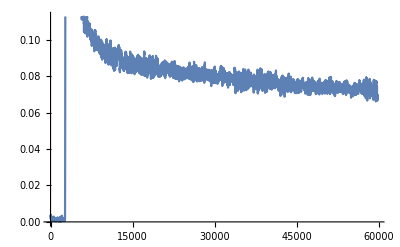

```mathematica
ListLinePlot[avfirstpeak[[9]]]
```

```mathematica
topdataav = topdata[[;;,2]];
Mean[topdataav];
```

{{{0,0.00009775,0.00502564,0.00364373},{6,0.0007874,0.00009775,0.00364373},{10,0.0030181,0.00312185,0.0024},{17,0.00009775,0.00199203,0.00260521},{21,0.00666667,0.00009775,0.00270812},11477,{59814,0.0980658,0.0024,0.00427699},{59818,0.0861818,0.00395939,0.00395939},{59824,0.100784,0.00148662,0.00009775},{59830,0.103984,0.00677789,0.00567596}},{1},{1},4,{1},{1}}
 |  |  |  |

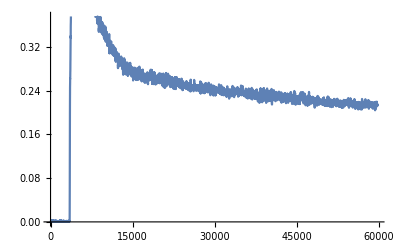

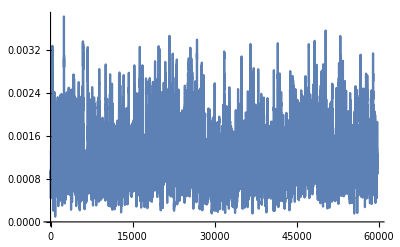

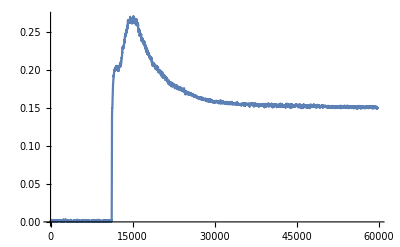

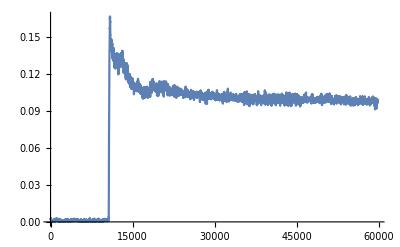

/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /almondmilk.txt

/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /soil1.txt

/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /tea.txt

/Users/tomi/Documents/GitHub/graphene-hack/mathematica_anlysis /oliveoil.txt

```mathematica
ListLinePlot[avfirstpeak[[8]]]
ListLinePlot[avfirstpeak[[3]]]
ListLinePlot[avfirstpeak[[2]]]
ListLinePlot[avfirstpeak[[1]]]
files[[1]]
files[[5]]
files[[8]]
files[[3]]
```